## Preliminaries

```mathematica
SetDirectory[NotebookDirectory[]];
<<mvrp.wl
<<mvrp_visualization.wl
setDir[]
```

C:\Users\Jaroslav Kysela\Dropbox\PhD studies\nova prace\wolfram appl\code samples\setups_Tue_13_9_2022

## Search

```mathematica
(*runSearch[10]*)
```

## Analysis

## Tests

```mathematica
ss={spdcNonColl[#1,2,2,3,g,False]&,phaseshift[#1,1,π/3]&,spdcColl[#1,2,1,g,False]&,phaseshift[#1,1,π]&,phaseshift[#1,2,π/3]&,phaseshift[#1,1,π/2]&,phaseshift[#1,3,π/2]&,spdcNonColl[#1,2,1,2,g,False]&,phaseshift[#1,2,π]&,phaseshift[#1,1,(2 π)/3]&};
```

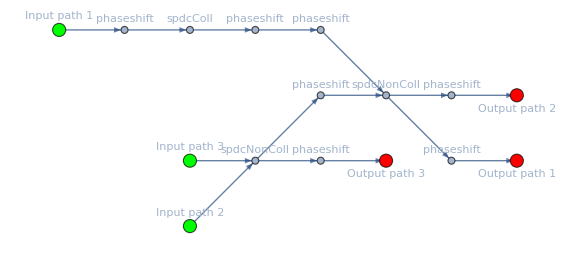

```mathematica
visualizeSetup[ss]
```

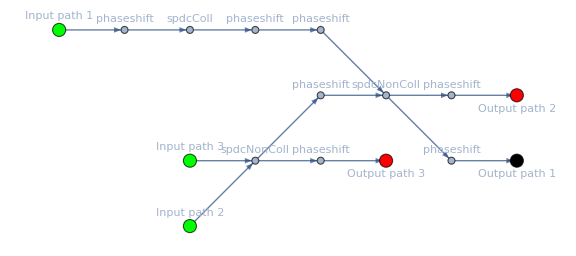

```mathematica
visualizeSetup[ss,{1,100}]
```

## Set Directory

```mathematica
(*SetDirectory[NotebookDirectory[]]*)
```

```mathematica
dir=;
SetDirectory[dir]
```

C:\Users\Jaroslav Kysela\Dropbox\stimulSPDC\setups_Thu_07_3_2019

```mathematica
files=FileNames[];
Length[files]
```

3

## Set file

```mathematica
file=;
(*file=files[[1]]*)
```

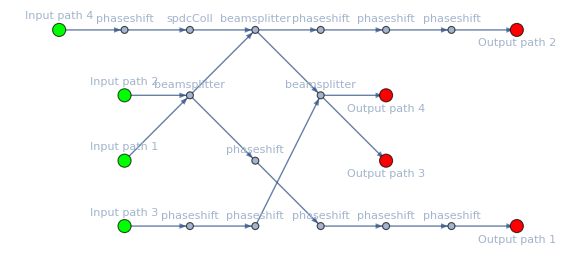
file name | C:\Users\Jaroslav Kysela\Dropbox\PhD studies\nova prace\wolfram appl\code samples\melvin\test_file.txt
visualization | -Graphics-
terms satisfying criteria | {{{},{}}}
unwanted parts in 1st order | {}
state complexity estimate | 0
coincidences triggering paths | {}
input state | β 1,0,0,0+α 1,1,0,0
reference patterns | {{α _ _,_,1,0,___,β _ _,_,1,1,___}}
highlighted first order | √2 α g 1,1,0,2+√2 β g 1,0,0,2
zero order | α 1,1,0,0+β 1,0,0,0
unwanted patterns in 1st order | {None}

```mathematica
analyzeSetup[file]
```